This notebook shows how to create bistability plots for the birdsfoot origami as seen in Fig. 2 of the paper “Robust folding of elastic origami”. The methods here are generalizable to any origami with two branches, although the target angle and sweep and identifyBranch[] function would need to be rewritten for the specific origami. This notebook requires the mechanisms.m package, located at [ https://github.com/cdsantan/mechanisms ]. If there are version incompatibilities, please email marvlee@umass.edu or cdsantan@syr.edu for an older version.

```mathematica
$HistoryLength=0;
SetDirectory[NotebookDirectory[]]
```

/Users/mel/Downloads

```mathematica
<<"mechanisms`"
```

```mathematica
$mechanismsVersion
```

0.85

## Origami Initialization

Start by creating a 6-fold symmetric origami:

```mathematica
m=changeCellData[_joint,"label"->"Index"]@singleVertex[{Pi/3,Pi/3,Pi/3,Pi/3,Pi/3,Pi/3}];
```

Then setup the linearized target angle sweep between the two branches and a vector of the true (not face) folds:

```mathematica
angles=(A) {M,0,M,-M,M,0}+(1-A) {-M,0,0,-M,0,0};
folds={{7,1},{7,3},{7,4},{7,5}};
```

Our next step is to find a list of points along the branches at various M. This will give us starting and ending points for sweeping between the two branches with the above minimization to establish bistability. To do this, start by creating a version of the birdsfoot that has zero programmed fold angle for all folds except the two that fold in both birdsfoot configurations.

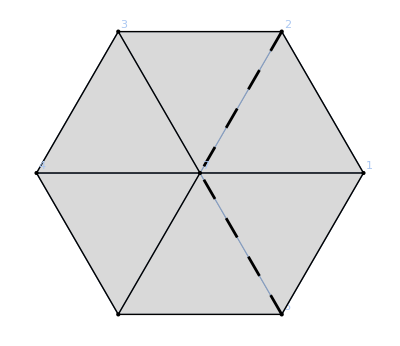

```mathematica
m1=changeCellData[rigidBar[{7,2}|{7,6}],"style"->{Thickness[0.005],Dashing[{0.04}]}]@addCells[m,{
fold[{7,1},{"angle"-> angles[[1]],"torsionalStiffness" -> kfold}],
fold[{7,2},{"angle"-> angles[[2]],"torsionalStiffness" ->0  kface}],
fold[{7,3},{"angle"-> angles[[3]],"torsionalStiffness" -> 0 kfold}],
fold[{7,4},{"angle"-> angles[[4]],"torsionalStiffness" -> kfold}],
fold[{7,5},{"angle"-> angles[[5]],"torsionalStiffness" -> 0 kfold}],
fold[{7,6},{"angle"-> angles[[6]],"torsionalStiffness" -> 0 kface}]
}]
```

Now simply minimize this origami at each end/start point of the sweep to get some initial guesses.

```mathematica
initialLeft=Quiet[Table[
en=mechanismEnergy[m1] /.{M->MM,kface->10^(-3),kfold->10^(-6)};
{energy1,pos1}=minimizeEnergy[m1,en/.A->0,Method->"QuasiNewton",MaxIterations -> 10^5];
{0,MM,{energy1,pos1}},
{MM,0.025,Pi,Pi/96}
]];
initialRight=Quiet[Table[
en=mechanismEnergy[m1] /.{M->MM,kface->10^(-3),kfold->10^(-6)};
{energy1,pos1}=minimizeEnergy[m1,en/.A->1,Method->"QuasiNewton",MaxIterations -> 10^5];
{1,MM,{energy1,pos1}},
{MM,0.025,Pi,Pi/96}
]];
```

```mathematica
normalVector[m,listFaces[m],"normalize"->False]
area=Sqrt[3]/2;
```

{{0,0,(√3)/2},{0,0,(√3)/2},{0,0,(√3)/2},{0,0,(√3)/2},{0,0,(√3)/2},{0,0,(√3)/2}}

```mathematica
m2=changeCellData[rigidBar,interiorEdges[m],"stiffness"->2 area/3]@changeCellData[rigidBar,boundaryEdges[m],"stiffness"->2 area/6]@changeCellData[rigidBar[{7,2}|{7,6}],"style"->{Thickness[0.005],Dashing[{0.04}]}]@addCells[m,{
fold[{7,1},{"angle"-> angles[[1]],"torsionalStiffness" -> kfold}],
fold[{7,2},{"angle"-> angles[[2]],"torsionalStiffness" -> kface}],
fold[{7,3},{"angle"-> angles[[3]],"torsionalStiffness" -> kfold}],
fold[{7,4},{"angle"-> angles[[4]],"torsionalStiffness" -> kfold}],
fold[{7,5},{"angle"-> angles[[5]],"torsionalStiffness" -> kfold}],
fold[{7,6},{"angle"-> angles[[6]],"torsionalStiffness" -> kface}]
}]
```

changeCellData::head: Bad cell type, rigidBar.

-Graphics-

## Functions

### mapLine[]

Takes end/start points from initialLeft and initialRight as defined above and follows the target angle sweep between the branches, minimizing the origami with the previous step as the initial condition until it reaches the other end point. Saves the energy and positions at each point.

```mathematica
mapLine[m2_,kfa_,kfo_][{0,MM_,{en1_,pos_}}]:=
Module[{en},
	en=mechanismEnergy[m2]/.{M->MM,kface->kfa,kfold->kfo};
	Rest@FoldList[{
		#2,MM,
		minimizeEnergy[m2,en/.A->#2,Method->"QuasiNewton",MaxIterations -> 10^5,"initial"-> #1[[3,2]]]
	}&,
		{0,MM,{en1,pos}},
		Range[0,1,0.00625]
	]
]

mapLine[m2_,kfa_,kfo_][{1,MM_,{en1_,pos_}}]:=Module[{en},
	en=mechanismEnergy[m2]/.{M->MM,kface->kfa,kfold->kfo};
	Rest@FoldList[{
		#2,MM,
		minimizeEnergy[m2,en/.A->#2,Method->"QuasiNewton",MaxIterations -> 10^5,"initial"-> #1[[3,2]]]
	}&,
		{1,MM,{en1,pos}},
		Range[1,0,-0.00625]
	]
]
```

### combineBranches[]

Takes the output of mapLine[] as input and combines the data so each point indexed by A and M has two saved energies and positions, one from each sweep direction.

```mathematica
combineBranches[ fromLeft_, fromRight_ ]:=
	joinBranchPoints/@Transpose[{fromLeft,Reverse[fromRight]}]

joinBranchPoints[ {{a_,b_,{e1_,p1_}},{aa_,bb_,{e2_,p2_}}} ] := {a,b,{e1,e2},{p1,p2}}
```

### identifyBranch[]

Identifies the branch the birdsfoot is in based on by the sign of the fold angle, which is sufficient for the birdsfoot.

```mathematica
ClearAll[identifyBranch];
identifyBranch[m_,{style1_,style2_,style3_}][{a_,b_,{e1_,e2_},{p1_,p2_}} ] := 
With[ { 
b1=Sign[Times@@foldAngle[m, p1, {{7,1},{7,4}}]], 
b2=Sign[Times@@foldAngle[m, p2, {{7,1},{7,4}}]] 
},
		Switch[ {b1,b2},
			{1,1},
				Flatten@{style1,Rectangle[{a-0.00625/2,b-Pi/192},{a+0.00625/2,b+Pi/192}]},
			{-1,-1},
				Flatten@{style2,Rectangle[{a-0.00625/2,b-Pi/192},{a+0.00625/2,b+Pi/192}]},
			{1,-1}|{-1,1},
				Flatten@{style3,Rectangle[{a-0.00625/2,b-Pi/192},{a+0.00625/2,b+Pi/192}]},
			_,
				{}
		]
]
```

## Data Run

An example of how to run the data in Fig. 2. The data is also saved in the GitHub, this does not need to be run for the rest of the notebook to work. This data includes the data necessary for full bistability plots for a grid of K_face from 10^(-1) to 10^(-3) and K_fold from 10^(-4) to 10^(-6).

```mathematica
Timing[data=Table[MapThread[
combineBranches[mapLine[m2, 10^(-i),10^(-j)][#1],mapLine[ m2,10^(-i),10^(-j)][#2]]&,
{
initialLeft,
initialRight
}
],{i,1,3,0.5},{j,4,6,0.5}];]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMinimum::lstol will be suppressed during this calculation.

FindMinimum::sdprec: Line search unable to find a sufficient decrease in the function value with MachinePrecision digit precision.

General::stop: Further output of FindMinimum::sdprec will be suppressed during this calculation.

{23738.8,Null}

## Data Analysis

Load data provided on GitHub or the one run above. If using above, use data[[2]] in place of “data2” to drop the time run.

```mathematica
data2=<<"fineMeshBistabilityData";
```

Plots all of the data that are in the paper, with relevant axes.

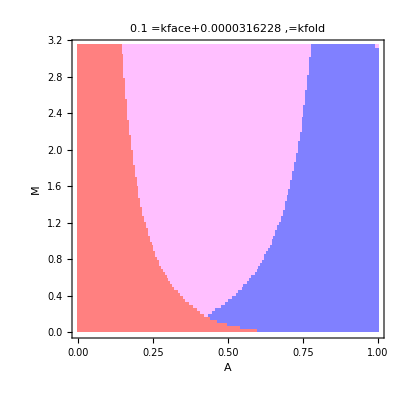
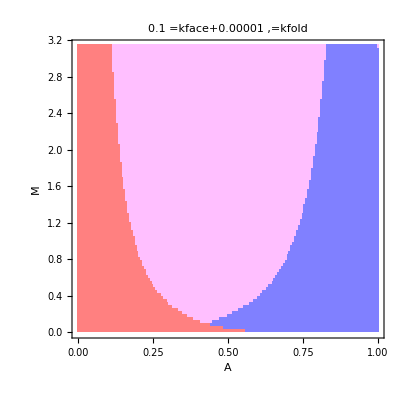
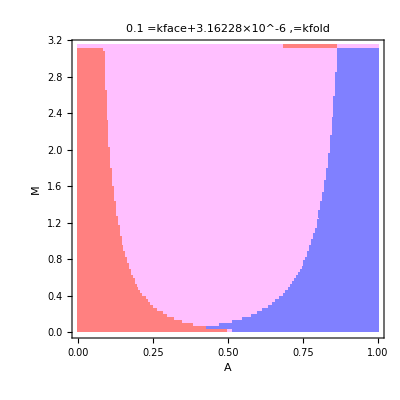
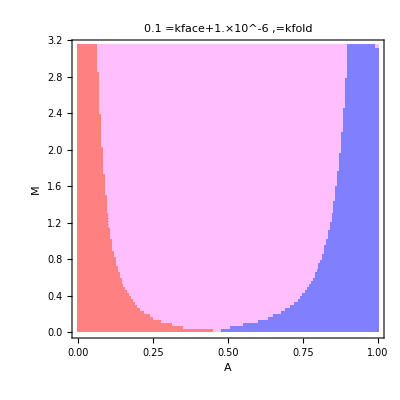
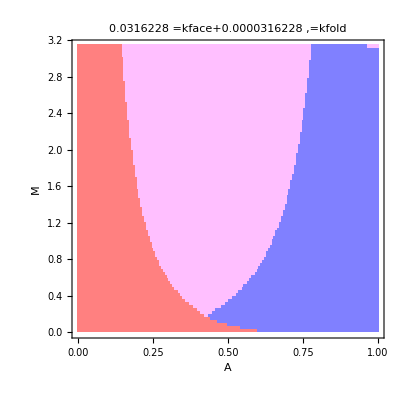
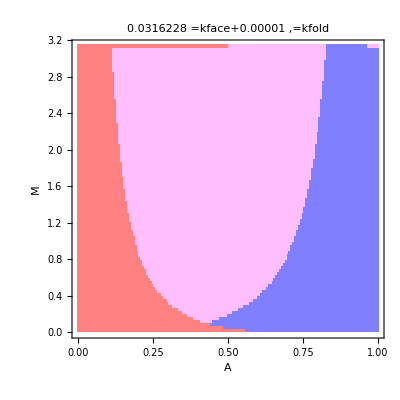
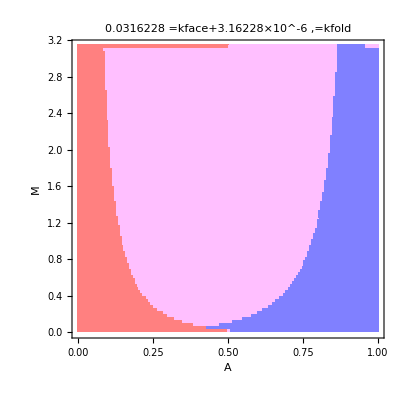
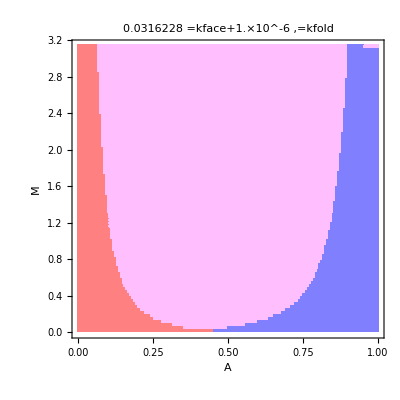
{1640.85,{{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-}}}

```mathematica
Timing[Table[Show[
ParametricPlot[{0,0},{A,0,1},{M,0,Pi},PlotRange->{{0,1},{0,Pi}},AspectRatio->1,PlotLabel->"=kface"10^(-((0.5)i+0.5))+",=kfold"10^(-((0.5)j+3.5)),FrameLabel->{"A","M"}],
Graphics[identifyBranch[m2,{{RGBColor[1,0.5,0.5]},{RGBColor[0.5,0.5,1]},{RGBColor[1,0.75,1]}}]/@Flatten[data2[[i,j]],1]]
],{i,1,5},{j,2,5}]]
```